```mathematica
Pmajority[n_,p_]:=(
k=Floor[n/2];
beta=BetaRegularized[1-p,n-k,k+1];
Return[1-beta];
)
```

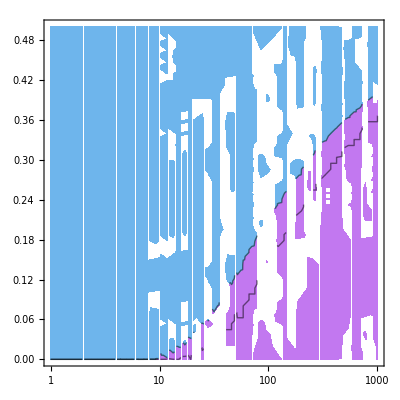

```mathematica
ContourPlot[Pmajority[n,p],
{n,1,1000},
{p,0,0.5},
Contours->{10^-20,10^-10},
ScalingFunctions->{"Log","Linear"},
ColorFunction->"Pastel"
]
```